## G(T) for p0=3.75

```mathematica
(*saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";*)
```

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p3.750/";
```

```mathematica
Directory[]
```

/home/chengling

```mathematica
Tlist={0.063 ,0.039, 0.03105 ,0.025 ,0.02,0.016 ,0.014,0.012,0.011,0.01,0.0093, 0.008 ,0.0063,0.005,0.00385};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,0.00930000,0.00800000,0.00630000,0.00500000,0.00385000}

```mathematica
spacing={22,22,23,25,40,34,400,400,400,247,400,287,393,400,400,400};
```

```mathematica
derivatives=Table[Table[Import[StringJoin[saveFolder,"SigmaSecD_N4096_p3.7500_T",Tstring[[T]],"_Spacing",ToString[spacing[[T]]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
g1=Table[Mean[Table[Mean[Normal[derivatives[[T,i,2]]][[Floor[Length[derivatives[[T,i,2]]]/2];;]]]/4096,{i,3}]],{T,Length[Tlist]}]
```

{0.741965,0.58808,0.523112,0.465745,0.409941,0.355336,0.320942,0.275636,0.251092,0.228001,0.213735,0.19105,0.164743,0.143155,0.122044}

```mathematica
g2=Table[Mean[Table[Variance[Normal[derivatives[[T,i,1]]*4096][[Floor[Length[derivatives[[T,i,2]]]/2];;]]],{i,3}]]/4096/Tlist[[T]],{T,Length[Tlist]}]
```

{0.541302,0.476831,0.435691,0.40896,0.378599,0.328808,0.304247,0.265896,0.241394,0.19775,0.214215,0.136959,0.0859052,0.0842281,0.0706463}

```mathematica
g1Mean=Table[Mean[Table[Mean[Normal[derivatives[[T,i,1]]*4096][[Floor[Length[derivatives[[T,i,2]]]/2];;]]],{i,3}]]/4096/Tlist[[T]],{T,Length[Tlist]}]
```

{-0.000805251,-0.0000992515,0.000034431,-0.000546891,0.000114737,0.000610911,-0.00107302,0.00257268,0.00215251,0.00258835,0.00399716,0.0811209,0.0422781,0.00625063,0.037048}

```mathematica
g1s=Table[Table[Mean[Normal[derivatives[[T,i,2]]][[Floor[Length[derivatives[[T,i,2]]]/2];;]]]/4096,{i,3}],{T,Length[Tlist]}]
```

{{0.741786,0.74199,0.742119},{0.587871,0.588096,0.588273},{0.523209,0.522985,0.52314},{0.465987,0.4656,0.465649},{0.409948,0.410006,0.409868},{0.355259,0.355417,0.355331},{0.320986,0.321122,0.320719},{0.275914,0.275386,0.275609},{0.251532,0.250655,0.25109},{0.228447,0.227403,0.228152},{0.212495,0.215326,0.213384},{0.189953,0.192607,0.190591},{0.164908,0.164182,0.165139},{0.144253,0.142571,0.142641},{0.122337,0.122197,0.121597}}

```mathematica
g2s=Table[Table[Variance[Normal[derivatives[[T,i,1]]*4096][[Floor[Length[derivatives[[T,i,2]]]/2];;]]],{i,3}]/4096/Tlist[[T]],{T,Length[Tlist]}]
```

{{0.536542,0.538772,0.548593},{0.481173,0.480463,0.468857},{0.434063,0.441595,0.431415},{0.406764,0.408317,0.411799},{0.386928,0.363858,0.38501},{0.330174,0.333176,0.323074},{0.303955,0.307279,0.301509},{0.267838,0.264277,0.265573},{0.236388,0.237213,0.250582},{0.196023,0.20518,0.192046},{0.217305,0.271678,0.153664},{0.0887847,0.229144,0.0929484},{0.0912248,0.0825648,0.0839262},{0.093987,0.0737283,0.084969},{0.066641,0.0797684,0.0655296}}

```mathematica
Length[derivatives[[11,1,2]]]/2
```

25000

```mathematica
Variance[Normal[derivatives[[11,3,1]]*4096][[Floor[Length[derivatives[[11,3,2]]]/2];;]]]/4096/Tlist[[11]]
```

0.153664

```mathematica
Mean[Normal[derivatives[[10,3,2]]][[Floor[Length[derivatives[[10,3,2]]]/2];;]]]/4096
```

0.228152

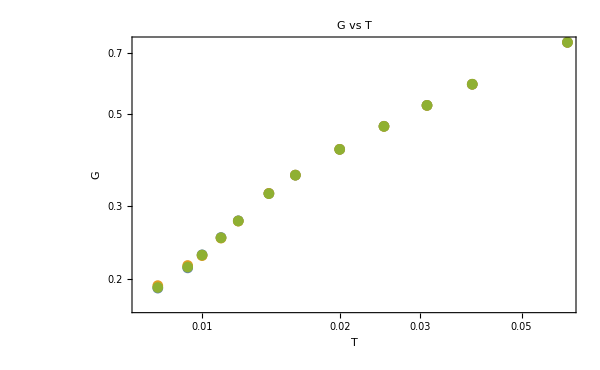

```mathematica
G1Plot=ListLogLogPlot[Table[Table[{Tlist[[T]],g1s[[T,i]]},{T,12}],{i,3}],FrameLabel->{"T","G"},ImageSize->600,PlotLabel->"G vs T"]
```

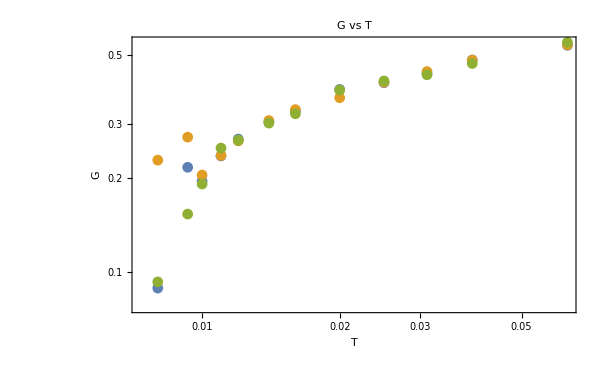

```mathematica
ListLogLogPlot[Table[Table[{Tlist[[T]],g2s[[T,i]]},{T,12}],{i,3}],FrameLabel->{"T","G"},ImageSize->600,PlotLabel->"G vs T"]
```

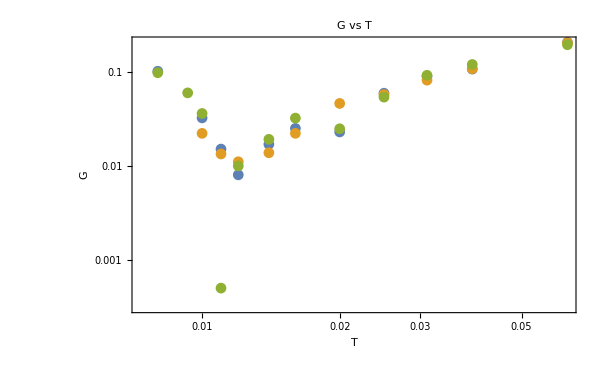

```mathematica
ListLogLogPlot[Table[Table[{Tlist[[T]],g1s[[T,i]]-g2s[[T,i]]},{T,12}],{i,3}],FrameLabel->{"T","G"},ImageSize->600,PlotLabel->"G vs T"]
```

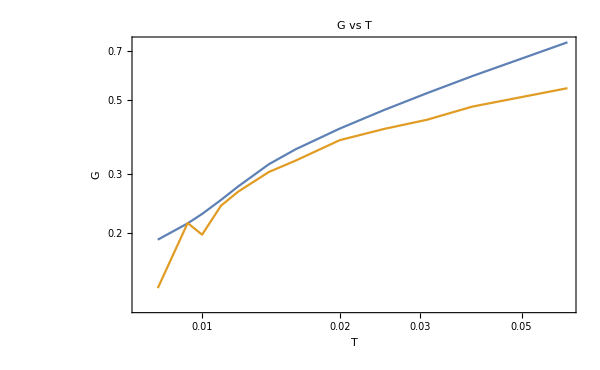

```mathematica
GPlot=ListLogLogPlot[{Table[{Tlist[[T]],g1[[T]]},{T,12}],Table[{Tlist[[T]],g2[[T]]},{T,12}]},FrameLabel->{"T","G"},ImageSize->600,PlotLabel->"G vs T",Joined->True,PlotLabel->{"G_1,G_2"}]
```

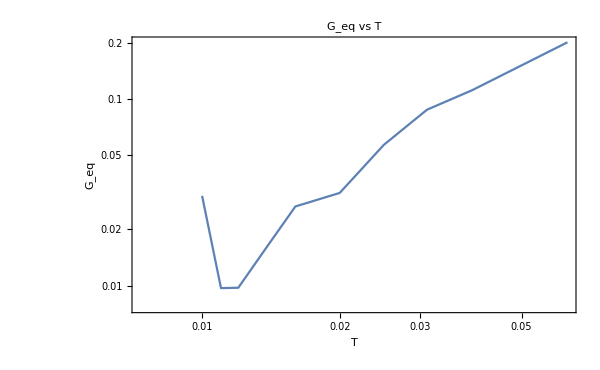

```mathematica
GeqPlot=ListLogLogPlot[Table[{Tlist[[T]],g1[[T]]-g2[[T]]},{T,12}],FrameLabel->{"T","G_eq"},ImageSize->600,PlotLabel->"G_eq vs T",Joined->True]
```

### fitting

```mathematica
GT[A_,T_,B_]:=A T^B;
```

```mathematica
g1fitting1=NonlinearModelFit[Table[{Tlist[[T]],g1[[T]]},{T,5}],{GT[A,t,B]},{A,B},t]
```

FittedModel[3.04179 t^0.508891]

```mathematica
g1fitting2=NonlinearModelFit[Table[{Tlist[[T]],g1[[T]]},{T,6,12}],{GT[A,t,B]},{A,B},t]
```

FittedModel[16.8174 t^0.930924]

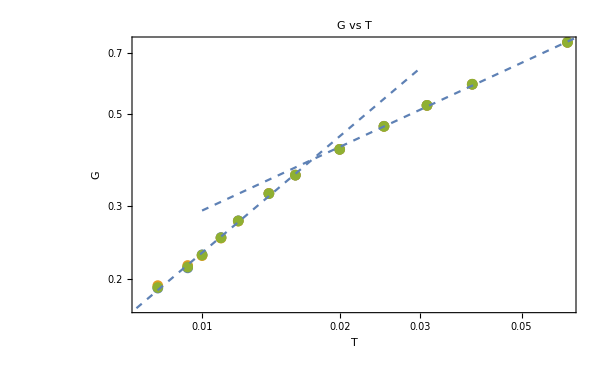

```mathematica
Show[G1Plot,LogLogPlot[g1fitting1[x],{x,0.01,0.1},PlotStyle->Dashed],LogLogPlot[g1fitting2[x],{x,0.0001,0.03},PlotStyle->Dashed]]
```

```mathematica
geqfitting=NonlinearModelFit[Table[{Tlist[[T]],g1[[T]]-g2[[T]]},{T,9}],{GT[A,t,B]},{A,B},t]
```

FittedModel[10.9883 t^1.43862]

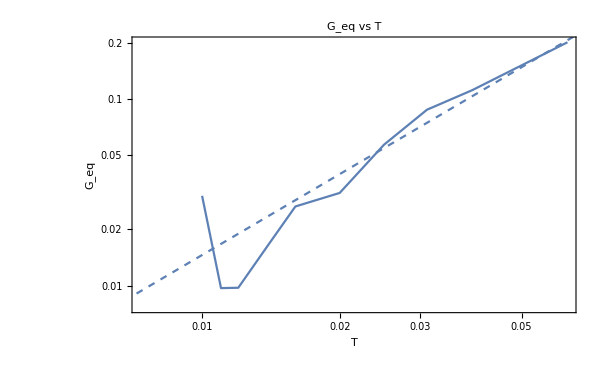

```mathematica
Show[GeqPlot,LogLogPlot[geqfitting[x],{x,0.0005,0.1},PlotStyle->Dashed,PlotLegends->Automatic]]
```

### G1, G2 as a function of averaging time

```mathematica
g1DA=Table[Mean[Table[Mean[Normal[derivatives[[1,i,2]]][[Floor[Length[derivatives[[1,i,2]]]/2];;length]]]/4096,{i,3}]],{length,Length[derivatives[[1,1,2]]]/2+100,Length[derivatives[[1,1,2]]],100}]
```

{0.741928,0.742749,0.742229,0.742969,0.743116,0.742899,0.743088,0.743118,0.74294,0.743098,0.742927,0.742894,0.742857,0.742653,0.742667,0.742705,0.742667,0.742769,0.742756,0.742723,0.742779,0.742732,0.742716,0.742601,0.742633,0.742652,0.742669,0.742605,0.742575,0.742564,0.742554,0.742429,0.742443,0.742437,0.74251,0.742557,0.74256,0.742545,0.742541,0.742447,0.74243,0.742369,0.742338,0.742426,0.742414,0.742386,0.742363,0.742349,0.742336,0.742278,0.742217,0.742212,0.742153,0.742145,0.742176,0.742157,0.742181,0.742161,0.742166,0.74217,0.742157,0.742177,0.742192,0.742197,0.742206,0.742161,0.742153,0.742172,0.742135,0.742126,0.742126,0.742143,0.742144,0.742155,0.74216,0.74216,0.742175,0.742173,0.742172,0.742172,0.742177,0.742166,0.742177,0.742196,0.74222,0.742254,0.74223,0.742227,0.74224,0.742235,0.74222,0.742223,0.742246,0.742253,0.742237,0.742245,0.742261,0.74225,0.74225,0.742259,0.742267,0.742276,0.742269,0.742261,0.742262,0.742251,0.742254,0.742261,0.742261,0.742246,0.742261,0.742264,0.742267,0.742253,0.742257,0.742243,0.742225,0.742221,0.742224,0.742216,0.742208,0.742209,0.742177,0.742183,0.742141,0.742115,0.742106,0.742114,0.742116,0.742106,0.742105,0.742112,0.742127,0.74212,0.742096,0.742093,0.742086,0.742072,0.742064,0.742058,0.742068,0.742044,0.742037,0.742055,0.742067,0.742071,0.742048,0.742043,0.742022,0.742019,0.742044,0.74202,0.742014,0.742003,0.742006,0.742007,0.741993,0.741999,0.742006,0.742009,0.742018,0.741995,0.741992,0.742019,0.742008,0.74201,0.742009,0.742001,0.742003,0.742019,0.742033,0.742053,0.742052,0.742051,0.742051,0.742039,0.74203,0.742032,0.742027,0.742021,0.742028,0.742023,0.742014,0.742008,0.742018,0.742017,0.742014,0.742012,0.742012,0.742003,0.742008,0.742001,0.742007,0.742022,0.742016,0.742013,0.742021,0.742016,0.742005,0.742011,0.742011,0.742009,0.741996,0.741991,0.741992,0.741999,0.741985,0.741973,0.741994,0.742016,0.742003,0.741997,0.741996,0.741993,0.741993,0.74198,0.741978,0.741978,0.741981,0.741974,0.741968,0.74196,0.741967,0.741963,0.741967,0.741965,0.741973,0.741975,0.741963,0.741965,0.74196,0.741964,0.741973,0.741974,0.741978,0.741985,0.741997,0.741992,0.741989,0.741981,0.741989,0.741979,0.741979,0.741977,0.74199,0.741983,0.741969,0.741962,0.741968,0.741965}

```mathematica
g2DA=Table[Mean[Table[Variance[Normal[derivatives[[1,i,1]]][[Floor[Length[derivatives[[1,i,2]]]/2];;length]]*4096]/4096/Tlist[[1]],{i,3}]],{length,Length[derivatives[[1,1,2]]]/2+100,Length[derivatives[[1,1,2]]],100}]
```

{0.443038,0.477529,0.521502,0.534866,0.533612,0.558351,0.562699,0.570749,0.560752,0.55682,0.557872,0.565078,0.564475,0.560834,0.567522,0.562869,0.559149,0.558458,0.56091,0.558872,0.557221,0.555618,0.55171,0.550672,0.548268,0.550273,0.549299,0.541947,0.541679,0.540436,0.538685,0.536588,0.536373,0.539065,0.539812,0.538775,0.537758,0.534862,0.536309,0.535864,0.534192,0.531659,0.531635,0.530333,0.531407,0.536269,0.534808,0.533029,0.532766,0.534306,0.531882,0.53313,0.533145,0.535907,0.53613,0.534391,0.534226,0.532051,0.530449,0.532227,0.533672,0.533621,0.533548,0.53212,0.532871,0.53563,0.534637,0.534562,0.53389,0.533393,0.535298,0.534354,0.535761,0.535148,0.536332,0.535641,0.534859,0.534952,0.534612,0.537226,0.539009,0.538444,0.538081,0.537599,0.53668,0.535797,0.537793,0.538004,0.536853,0.537194,0.537085,0.53783,0.540086,0.542401,0.542618,0.543098,0.544454,0.544826,0.545846,0.546242,0.547127,0.548036,0.547834,0.546997,0.547846,0.548461,0.549065,0.548535,0.547889,0.547354,0.547719,0.546995,0.548907,0.548573,0.547817,0.548572,0.548577,0.549155,0.548911,0.548017,0.548014,0.548099,0.547715,0.547207,0.54774,0.5477,0.546932,0.547249,0.546893,0.546065,0.546812,0.545522,0.545956,0.546542,0.545981,0.546528,0.545845,0.545143,0.544357,0.542685,0.54177,0.543809,0.543558,0.542901,0.543436,0.543089,0.542992,0.542855,0.54226,0.542441,0.542954,0.543277,0.543186,0.542313,0.5427,0.543164,0.542832,0.542648,0.542901,0.542653,0.54376,0.543163,0.543512,0.542929,0.543195,0.542965,0.54302,0.542062,0.542382,0.542065,0.541804,0.541313,0.541948,0.541895,0.54216,0.542229,0.542871,0.543276,0.543193,0.542295,0.542101,0.541642,0.541264,0.541043,0.54077,0.54054,0.541329,0.541289,0.54105,0.540669,0.539841,0.540291,0.540523,0.539906,0.539678,0.539729,0.53959,0.540658,0.540471,0.540888,0.541788,0.54119,0.54067,0.540634,0.540505,0.540705,0.541088,0.54113,0.541246,0.541128,0.541423,0.541654,0.541644,0.542324,0.541976,0.541534,0.541415,0.540944,0.540758,0.541281,0.541133,0.541445,0.541028,0.541549,0.542019,0.542296,0.542927,0.54227,0.54199,0.541344,0.541675,0.542067,0.54201,0.541907,0.542124,0.542285,0.542051,0.54214,0.542179,0.54207,0.542163,0.541862,0.541637,0.541798,0.541625,0.541985,0.541621,0.541481,0.541197,0.541302}

```mathematica
timesteps=Table[length-Length[derivatives[[Length[Tlist],1,2]]]/2,{length,Length[derivatives[[Length[Tlist],1,2]]]/2+100,Length[derivatives[[Length[Tlist],1,2]]],100}];
```

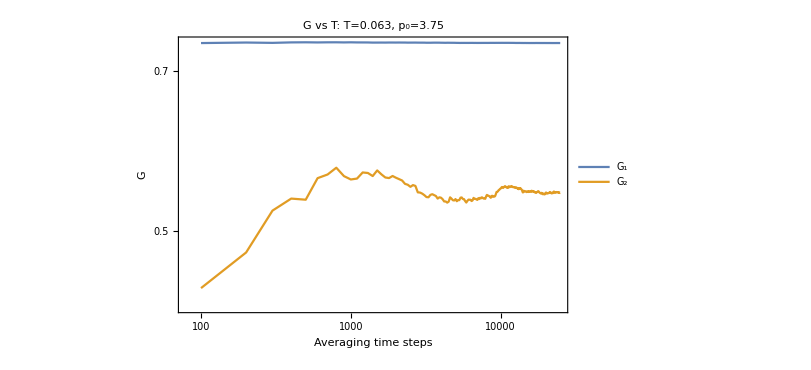

```mathematica
ListLogLogPlot[{Table[{timesteps[[t]],g1DA[[t]]},{t,Length[timesteps]}],Table[{timesteps[[t]],g2DA[[t]]},{t,Length[timesteps]}]},FrameLabel->{"Averaging time steps","G"},ImageSize->600,PlotLabel->"G vs T: T="<>ToString[Tlist[[1]]]<>", p_0=3.75",Joined->True,PlotLegends->{"G_1","G_2"}]
```